## ψ_(++)(x_1,x_2), ψ_(+-)(x_1,x_2), ψ_(-+)(x_1,x_2) and ψ_(--)(x_1,x_2)

```mathematica
ψ1[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 + σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n! 2^n))HermiteH[n,(x1+x2)/(√2)];, ψ_(++)
ψ2[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(σ1 -n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ3[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ (σ2 + n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(-ⅈ 2θ))^k Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
ψ4[n_,x1_,x2_,σ1_,σ2_,θ_]:=(ⅇ^(ⅈ(-n θ))ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!2^n))HermiteH[n,(x1+x2)/(√2)];
ψ[n_,x1_,x2_,σ1_,σ2_,θ_]:=-(ⅇ^(-(x1^2+x2^2)/2))/(4 √(π  n!))∑_(k=0)^n (ⅇ^(ⅈ(σ1 + σ2 + n θ))+(ⅇ^(ⅈ 2θ))^k ⅇ^(ⅈ(σ1 -n θ))+(ⅇ^(-ⅈ 2θ))^k ⅇ^(ⅈ (σ2 + n θ))+ⅇ^(ⅈ(-n θ)))Binomial[n,k]/2^n HermiteH[n-k,x1]HermiteH[k,x2];
```

## Effects of losses (Assumption: ψ_(+-)(x,x) and ψ_(-+)(x,x) amplitudes are negligible after post selection on x=√N)

```mathematica
P[j_,n_,x_,σ1_,σ2_,θ_,t_,R_]:=Module[{f,α,β,ψpp,ψmm,outPhase},
outPhase={{1,ⅈ^2,ⅈ^2,ⅈ^4},{ⅈ,ⅈ^3,ⅈ,ⅈ^3},{ⅈ,ⅈ,ⅈ^3,ⅈ^3},{ⅈ^2,ⅈ^2,ⅈ^2,ⅈ^2}};
α=ⅈ √(1-t^2)R/(√2)ⅇ^(+ⅈ θ);
β=ⅈ √(1-t^2)R/(√2)ⅇ^(-ⅈ θ);
f=ⅇ^(-(Abs[β]^2+Abs[α]^2+2β* α));
ψpp=ψ1[n,x,x,σ1,σ2,θ];
ψmm=ψ4[n,x,x,σ1,σ2,θ];
Abs[ t^n ⅇ^((1-t^2)R^2/2)]^2(Abs[outPhase[[j,1]]ψpp]^2+Abs[outPhase[[j,4]]ψmm]^2+2Re[ f (outPhase[[j,1]]ψpp)* (outPhase[[j,4]]ψmm)])
];
```

NOTE : This expression is sensitive to R, whereas earlier we had seen that R can be arbitrary.
This arises while making the assumption that a single coherent state can be pulled out of the integral over ϕ.

#### Plots

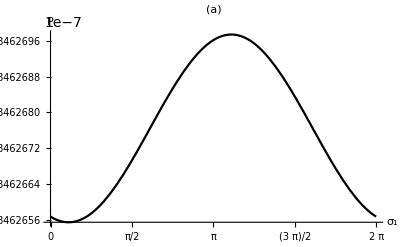

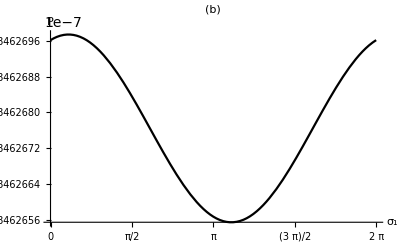

```mathematica
t=0.6;
n=24;R=√n;p1=Plot[P[4,n,√n,σ1,0,π/4,t,R],{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->30]]
p2=Plot[P[4,n,√n,σ1,π,π/4,t,R],{σ1,0,2π},ImageSize->Scaled[1],PlotRange->Full,AxesStyle-> Black,AxesLabel->{"σ_1","P"},LabelStyle->{FontSize->30,FontFamily->"Times", Black},Ticks->{Range[0,2Pi,Pi/2],Automatic},PlotStyle->Black,PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->30]]
```

## CHSH Bell’s inequality considering loss (and no binning for homodyne measurement)

### Calculating the expectation value:- ⟨ab⟩

```mathematica
LossyExpec1[n_,σ1_,σ2_,θ_,t_,R_]:=
Module[{i,j,k,l},
i=P[1,n,√n,σ1,σ2,θ,t,R];
j=P[2,n,√n,σ1,σ2,θ,t,R];
k=P[3,n,√n,σ1,σ2,θ,t,R];
l=P[4,n,√n,σ1,σ2,θ,t,R];
N[(i-j-k+l)/(i+j+k+l)]];
LossyS1[n_,θ_,a_,b_,aprime_,bprime_,t_,R_]:=Abs[LossyExpec1[n,a,b,θ,t,R]+LossyExpec1[n,a,bprime,θ,t,R]+LossyExpec1[n,aprime,b,θ,t,R]-LossyExpec1[n,aprime,bprime,θ,t,R]];
```

## Plots

#### S should not be sensitive to R. This is expected as the number state written in terms of coherent states on a circle allows for arbitrary R.

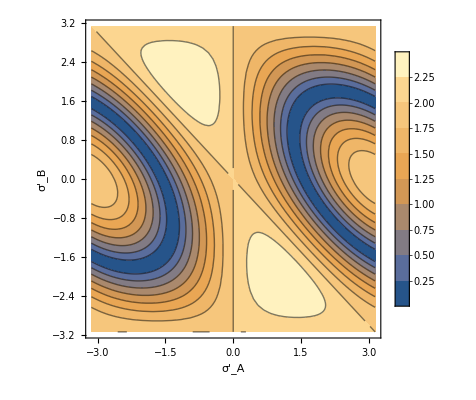

```mathematica
n=24;
t=1;
R=1;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

```mathematica
n=24;
t=1;
R=√24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

-Graphics-

```mathematica
n=24;
t=1;
R=24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

-Graphics-

#### For t = 1 we see that S is independent of R

## Now we look at the case where t ≠ 1 (losses) with the approximation

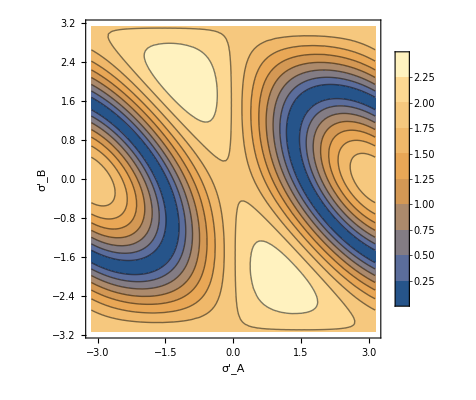

```mathematica
n=24;
t=0.99;
R=1;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

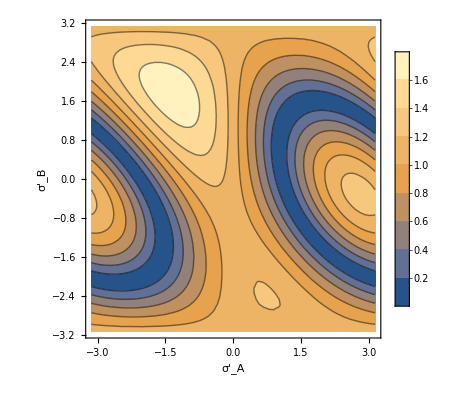

```mathematica
n=24;
t=0.99;
R=√24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

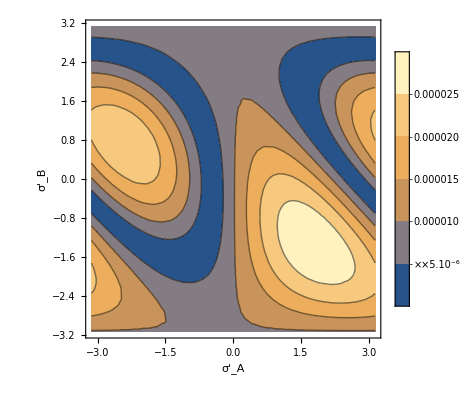

```mathematica
n=24;
t=0.99;
R=24;
ContourPlot[LossyS1[n,π/4,0,π,aprime,bprime,t,R],{aprime,-π,π},{bprime,-π,π},PlotLegends->Automatic, Axes->True,GridLines->Automatic, AxesStyle->Thick,LabelStyle->{FontSize->18,FontFamily->"Times",Black},AxesLabel->{"σ'_A","σ'_B"},Ticks->{Range[0,2Pi,Pi/2],Range[-Pi,Pi,Pi/2]}]
```

As R is arbitrary, we can choose R>>1 so the approximations are valid. However, we see that for large R, S drops rapidly.